```mathematica
theoreticalColor="TropicalRainForest";
experimentalColor="BrickRed";
```

```mathematica
theoList={{0.5,0.0403},{1.67, 0.074},{8,0.36},{13,0.624},{15,0.78},{16.7, 0.8714},{18,0.904}}
```

{{0.5,0.0403},{1.67,0.074},{8,0.36},{13,0.624},{15,0.78},{16.7,0.8714},{18,0.904}}

```mathematica
experimentalList={{0.5,23/1000},{1.67, 78/1000},{2,95/1000 },{6,288/1000},{8,391/1000},{10,469/1000},{16.7, 893/1000}}
```

{{0.5,23/1000},{1.67,39/500},{2,19/200},{6,36/125},{8,391/1000},{10,469/1000},{16.7,893/1000}}

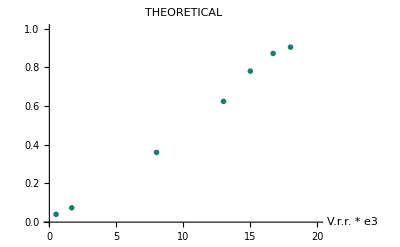

```mathematica
PlotTheoretical=ListPlot[theoList, 
PlotStyle->{ColorData["Crayola"][theoreticalColor],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,20},{0,1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"THEORETICAL"]
```

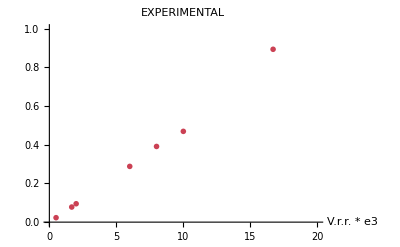

```mathematica
PlotExperimental=ListPlot[experimentalList, 
PlotStyle->{ColorData["Crayola"][experimentalColor],Thickness[0.010]},
PlotMarkers->{{●,10}},PlotRange->{{0,20},{0,1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"EXPERIMENTAL"]
```

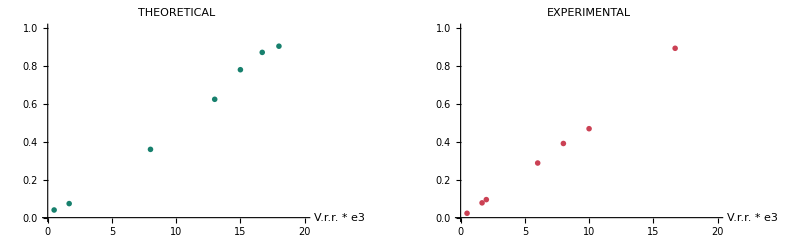

```mathematica
GraphicsRow[{PlotTheoretical, PlotExperimental}]
```

```mathematica
Rasterize[ListPlot[{theoList,experimentalList},
PlotLegends->{"theoretical","experimental"},PlotStyle->{{ColorData["Crayola"][theoreticalColor],Thickness[0.01]}, {ColorData["Crayola"][experimentalColor],Thickness[0.01]}},
PlotLabel->Style["Probability of extinction",20,FontOpacity->0.999],
Frame->True,
FrameLabel->{Style["Virus removal rate * E3",15,FontOpacity->0.999],""},
LabelStyle->Directive[FontFamily->"Times",Black,FontSize->15]]]
```

-Graphics-